# Introduction to Technical Computing with Mathematica

## Introduction to Cells

In Mathematica code and text are organized in a notebook file. A cell can contain text (title, subtitle, chapters, sections, etc.), code and even Wolfram Alpha search queries. In this document we have started with creating a title cell, a chapter cell and this text cell. Organizing your notebook in chapters, sections and subsections is very useful, since we can collapse the content of each of them which makes larger notebooks more organized. To achieve this “double click” on the outer bracket of the chapter or section cell.

Learning all the Mathematica shortcuts increases speed and we will document the ones that we are using most of the time. A full list of shortcuts is provided in the official Mathematica documentation (https://reference.wolfram.com/language/tutorial/KeyboardShortcutListing.html).

Alt (Option) + Enter:	creates a new cell below the current one using the same style as the current cell

Alt (Option) + 1:		changes the style of the current cell to “Title”

Alt (Option) + 2:		changes the style of the current cell to “Chapter”

Alt (Option) + 3:		changes the style of the current cell to “Subchapter”

Alt (Option) + 4:		changes the style of the current cell to “Section”

Alt (Option) + 5:		changes the style of the current cell to “Subsection”

Alt (Option) + 6:		changes the style of the current cell to “Subsubsection”

Alt (Option) + 7:		changes the style of the current cell to “Text”

Alt (Option) + 8:		changes the style of the current cell to “Code”

Alt (Option) + 9:		changes the style of the current cell to “Input”

Shift + Enter:		evaluates the current input cell

Shift + Ctrl + D:		divides cell

Shift + Ctrl + M:		merges cells

Shift + Ctrl + E:		shows expression

Ctrl + B:			write in bold, pressing again causes the next text to be in normal style again

Ctrl + I:			write in italic, pressing again causes the next text to be in normal style again

Ctrl + U:			underline the text

The usual shortcuts for “copy, paste, cut, undo, redo, etc.” are the same as in other editors.

## LATEX formatting shortcuts

Pressing “Ctrl + (” opens the inline math mode of Mathematica. Close it by pressing “Ctrl + )”. Using LATEX \mathcal and \mathbb can be done by pressing “Esc + sc + WHATEVER + Esc”.

## Include Wolfram Alpha Search Results

The cool thing about Mathematica notebooks is that we can mix code, calculations, text and even search results from Wolfram Alpha. Imagine the following setup: we want to explore some graph theoretic phenomenon but we want to include the official definitions, examples or even the current state of research in the same place. This can be done easily using Mathematica. Formatting certain parts of a text cell in math mode is very convenient in Mathematica. Do the following inside a text cell.

Press “Ctrl + (” to enter inline math mode

Press “Ctrl+ )” to leave math mode

Entering special characters such as greek letters is possible in math mode by first pressing “Esc” and then entering the greek letter, e.g. “chi”., and then entering “Esc” again

A full reference can be found in the officical Mathematica documentation:

Math in Text: https://reference.wolfram.com/language/workflow/InsertInlineMathInText.html

Notice that it is also possible to use inline LATEX by pressing “Ctrl+$” and then press “Enter” to interpret the result.

Mathematical Notation Characters: https://reference.wolfram.com/language/guide/MathematicalNotationCharacters.html

Greek letters: https://reference.wolfram.com/language/guide/GreekLetters.html

Definition: A graph G is perfect if ω(H)=χ(H) for each induced subgraph H of G.

Now, imagine that we also want to display the informations that Wolfram Alpha provides for perfect graphs. Create a new input cell and type “==” and just enter a search phrase. Then evaluate the search cell by just pressing “Enter”.

perfect graphs

WolframAlphaQueryResults

Let us suppose that we want to provide a reference to the strong perfect graph theorem as well.

strong perfect graph theorem

WolframAlphaQueryResults

Now, let us suppose that we do not now what an odd hole is. This is no problem.

graph hole

WolframAlphaQueryResults

Since Wolfram Alpha does not include a picture of an odd hole, let us use the builtin graph generators of Mathematica.

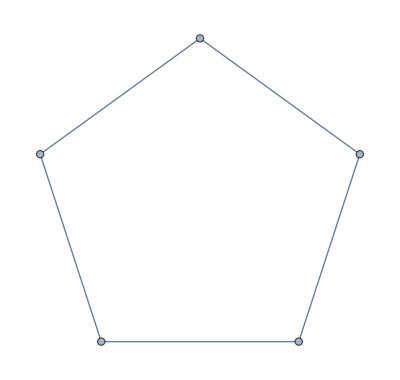

```mathematica
GraphPlot[CycleGraph[5]]
```

It is well known that the complement of the shortest odd hole on 5 vertices is isomorphic to its complement. Thus, let us generate the odd antihole on 7 vertices.

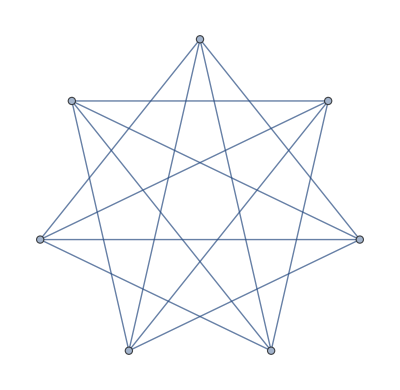

```mathematica
GraphPlot[GraphComplement[CycleGraph[7]]]
```

Let us generate all odd anti-holes up to 20 vertices and put them in a table.

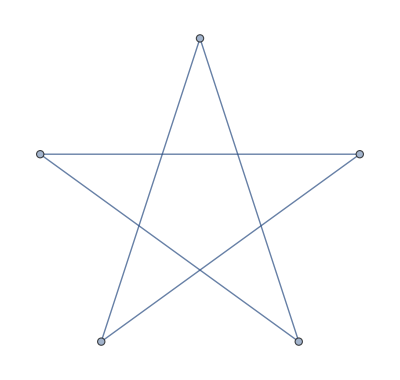
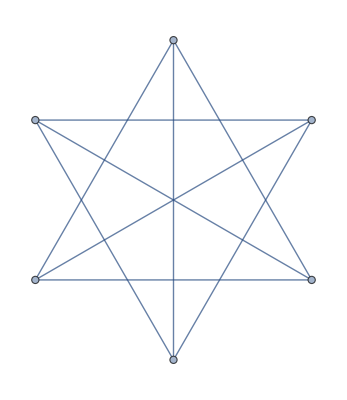
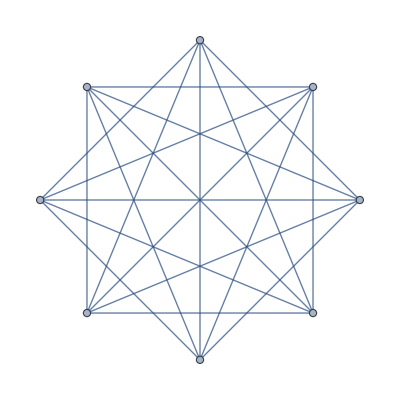
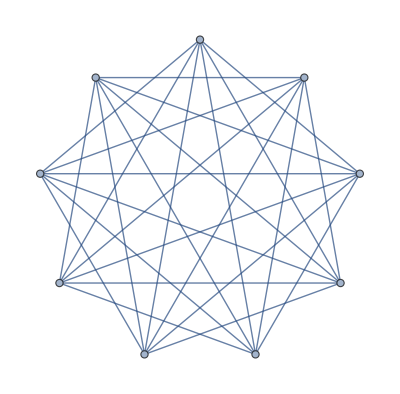
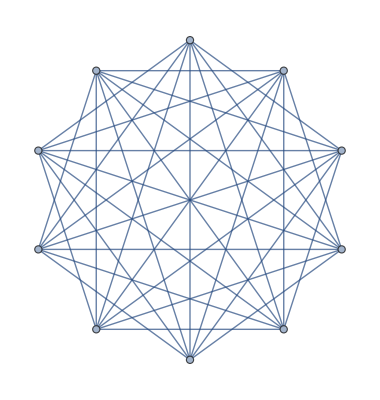
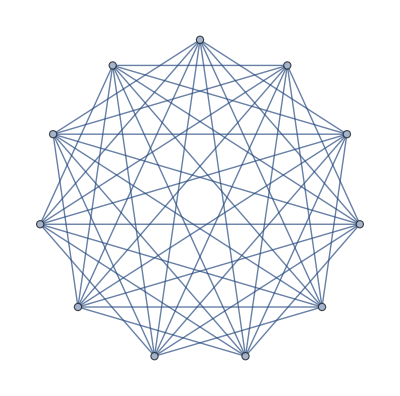
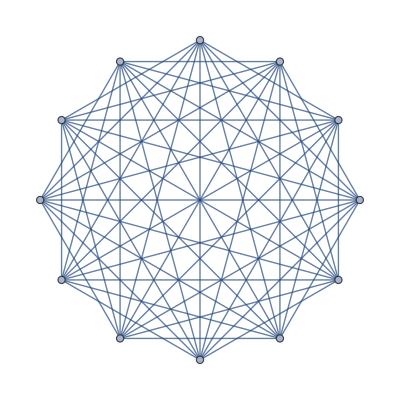
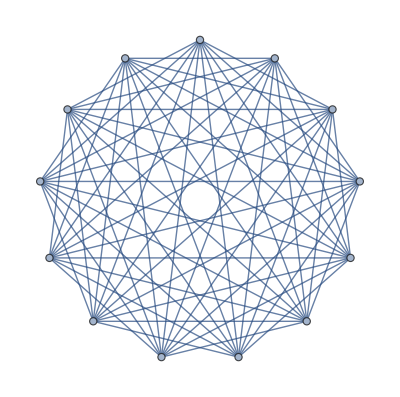
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[GraphComplement[CycleGraph[n]],{n, 5, 20}]
```

## Arithmetic

Of course we can use basic arithmetic in Mathematica. Here are some examples.

```mathematica
1 + 2
```

3

```mathematica
3*4(12+1)*23
```

3588

```mathematica
20/3
```

20/3

Notice that Mathematica always evaluates to the simplest exact form, e.g. 20/3 is not further evaluated. Suppose that we want to get an approximate value. This is simple.

```mathematica
N[20/3]
```

6.66667

Suppose that we want to include more than 5 digits. This is also simple.

```mathematica
N[20/3, 20]
```

6.6666666666666666667

Basic constants are of course builtin .

```mathematica
Pi
```

π

```mathematica
N[Pi, 10]
```

3.141592654

```mathematica
Sqrt[2]
```

√2

```mathematica
N[Sqrt[2], 35]
```

1.4142135623730950488016887242096981

## The Kernel

Mathematica sends the input from our notebook to a backend kernel which does the actually evaluation. We can access the last evaluation as follows.

```mathematica
Pi
```

π

```mathematica
Out[35]
```

π

```mathematica
1 + 1
```

2

```mathematica
Out[37] + 5
```

7

Restarting the kernel is simple as well, e.g. if we want to interrupt a long running calculations. The shortcut is “Option + Dot”.

## Core Language Features

In this section we are going to give an overview of the core language features. First, everything in Mathematica is an expression. The expression “FullForm” displays the full form of a given expression, which is useful in some scenarios.

```mathematica
FullForm[3 +x]
```

Plus[3,x]

An expression consist of a head and of its arguments in square brackets. We can get the head of an expression using the head function as follows.

```mathematica
Head[3+x]
```

Plus

The arguments are the parts of an expression.

```mathematica
Part[3+x, 1]
```

3

```mathematica
Part[3+x,2]
```

x

In general, an expression in Mathematica looks as a function with two arguments f[x, y].

```mathematica
? Apply
```

Using the above, we can replace the head with something else. Consider the following.

```mathematica
Apply[List, 3+x]
```

{3,x}

What has happened above? We have replace the Plus head of the expression by a List, thus a list of its arguments (3 and x) is returned.

There is a shorthand notation for the above which is @@. Consider the following.

```mathematica
Plus @@ {1,2,3}
```

6

The above replaces the head of the list 1,2,3 by Plus, thus 1+2+3 is returned.

### Lists

Lists are a fundamental concept in Mathematica. They are used all the time. Let us evaluate the most important basics about lists.

Lists are defined with curly braces, for example.

```mathematica
{1, 2, 3}
```

{1,2,3}

We can mix list with all different kinds of objects, for example.

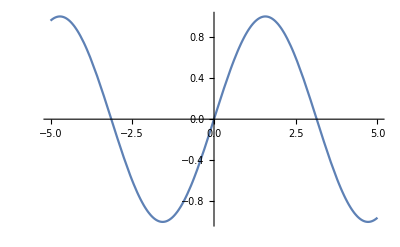
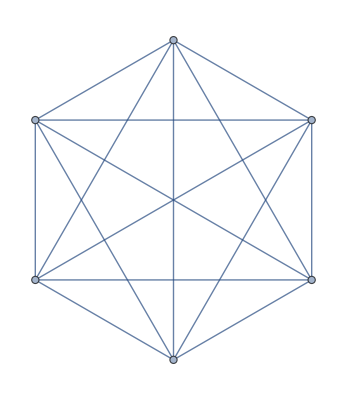
{a,2,3,2.3,cat,-Graphics-,-Graphics-}

```mathematica
list = {a ,2 ,3, 2.3, "cat", Plot[Sin[x], {x, -5, 5}, ImageSize->Tiny],  CompleteGraph[6]}
```

```mathematica
? Range
```

```mathematica
Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

We can add an element to each element of the list as follows.

```mathematica
Range[10]+x
```

{1+x,2+x,3+x,4+x,5+x,6+x,7+x,8+x,9+x,10+x}

Notice that the above works for all mathematical operators, such as multiplication or sqrt, e.g.

```mathematica
Sqrt[Range[10]]
```

{1,√2,√3,2,√5,√6,√7,2 √2,3,√10}

In most programming languages, we would need to create a loop and then apply the operator to each element of the list. This is not necessary in Mathematica. It uses a concept called vectorized functions that allow us to apply a function to a list without the need for creating a loop. We will create our own vectorized functions in the section about functions.

However, notice that it is not possible to add two lists together whose size is different; the same holds for all operators.

We can create generating lists using the table function.

```mathematica
? Table
```




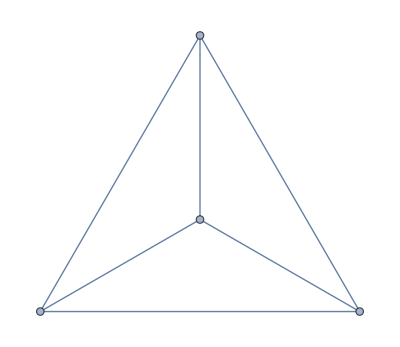

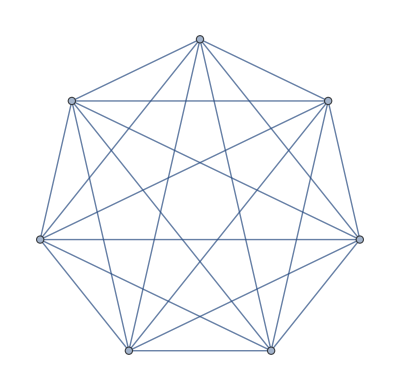
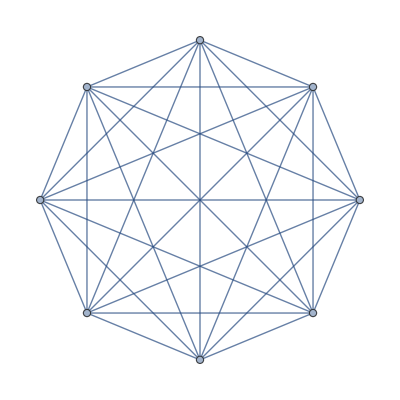
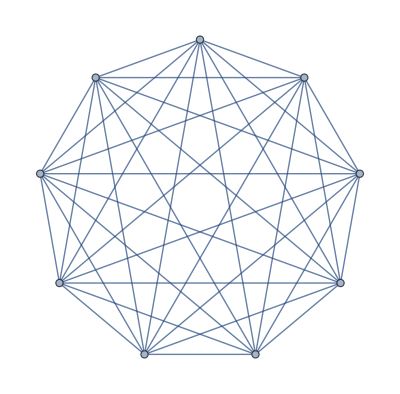
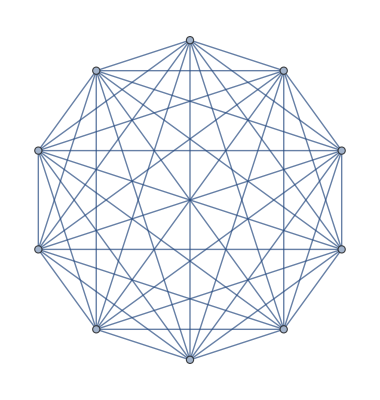
{{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-},{-Graphics-}}

```mathematica
Table[{CompleteGraph[n]}, {n, 1, 10}]
```

Using the table function it is neatly possible to combine two different lists as follows.

```mathematica
a = Table[CompleteGraph[n], {n, 1, 10}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

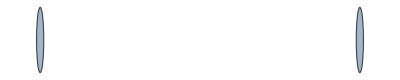
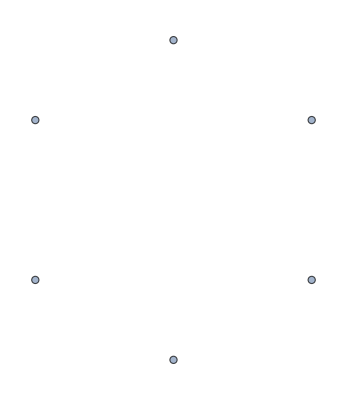
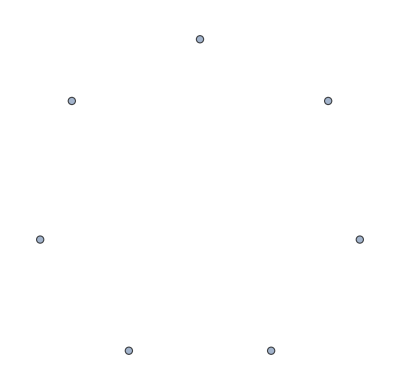
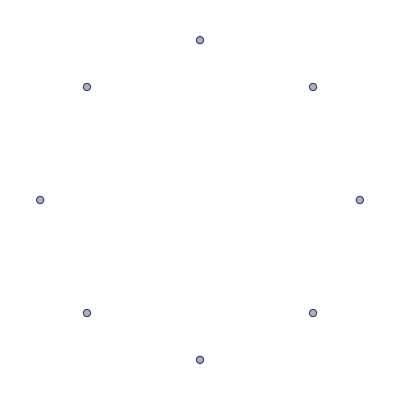
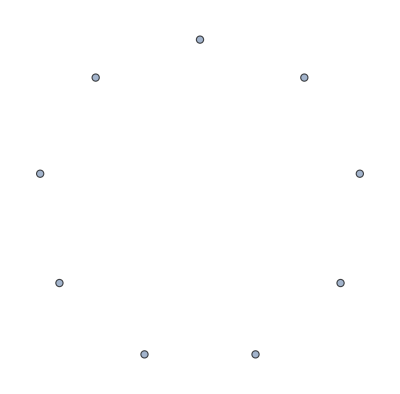
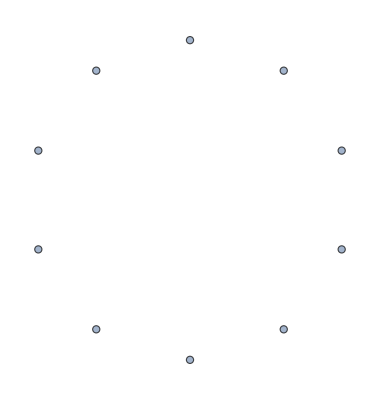
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
b = Table[GraphComplement[CompleteGraph[n]], {n, 1, 10}]
```

```mathematica
pairs = Table[{a[[i]], b[[i]]}, {i,Length[a]}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
? Depth
```

We can use postfix notation to display a list in matrix form as follows.

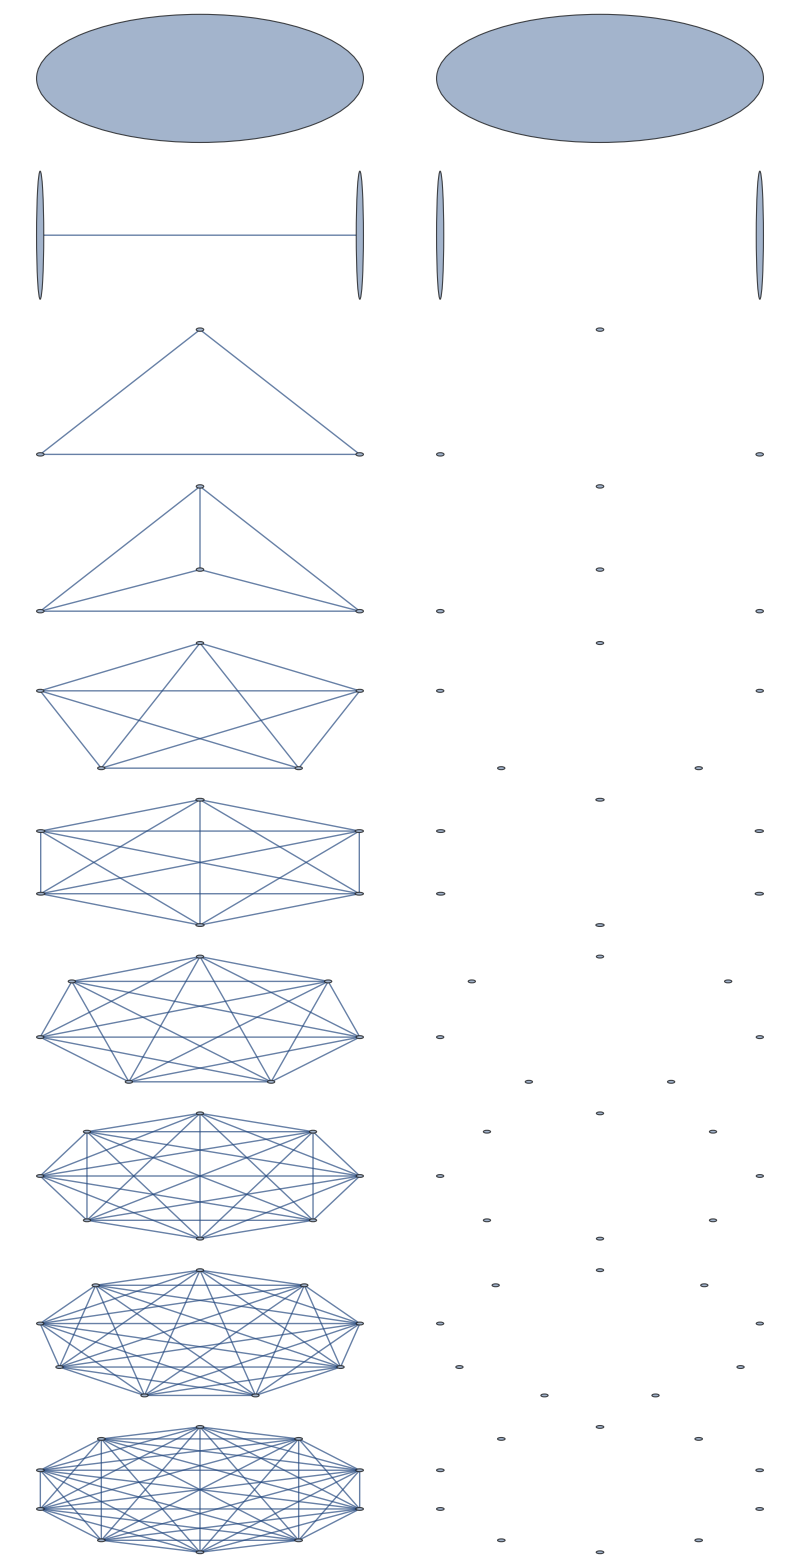
(-Graphics-)

```mathematica
pairs // MatrixForm
```

We could also create a grid using the Grid function as follows.

```mathematica
Grid[pairs]
```

-Graphics-

We could change the colour and add a frame using rules as follows.

```mathematica
Grid[pairs, Frame -> All, Background->Lighter[Gray, 0.9]]
```

-Graphics-

### Flattening and Partitioning

```mathematica
? Flatten
```

```mathematica
flattenPairs=Flatten[pairs, 1]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

This is also possible the other way around, say we want to turn a flatten list into a nested list . We can achieve this using the partition function.

```mathematica
? Partition
```

```mathematica
Partition[flattenPairs,2]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Accessing List Elements

```mathematica
? Part
```

```mathematica
Part[pairs, 1]
```

{-Graphics-,-Graphics-}

```mathematica
Part[pairs, 2]
```

{-Graphics-,-Graphics-}

For getting the last element, we use a negative index.

```mathematica
pairs[[-1]]
```

{-Graphics-,-Graphics-}

Since this is a pair, we want the second element from the last pair using the following.

```mathematica
pairs[[-1]][[2]]
```

-Graphics-

Since this is a little hard to read, we can use a shorthand notation as follows.

```mathematica
pairs[[-2, 2]]
```

-Graphics-

```mathematica
? Take
```

```mathematica
Take[pairs, 4]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
Take[pairs, {1, 4}]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

```mathematica
? Span
```

We can achieve the same thing using the Span function as follows.

```mathematica
Part[pairs, Span[1,4]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

There is a shorthand notation for this as well. It works as follows.

```mathematica
pairs[[;;4]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

Or if we want to get the elements from 3 to 6, there is also a shorthand notation. It works as follows.

```mathematica
pairs[[3;;6]]
```

{{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-},{-Graphics-,-Graphics-}}

### Modifying lists

Let us generate the alphabet.

```mathematica
alphabet = Alphabet[]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Notice that lists in Mathematica are immutable. Thus using the append function we can append elments to a list, but we need to save the result in a new list.

```mathematica
appendToAlphabet = Append[alphabet, "Hallo Welt"]
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Hallo Welt}

```mathematica
alphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
appendToAlphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Hallo Welt}

We can prepend elements to a list as follows.

```mathematica
prependToAlphabet = Prepend[appendToAlphabet, "Hallo Prepend"]
```

{Hallo Prepend,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Hallo Welt}

```mathematica
appendToAlphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Hallo Welt}

```mathematica
alphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
prependToAlphabet
```

{Hallo Prepend,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,Hallo Welt}

We can insert at specific positions, and delete elements as follows.

```mathematica
Delete[alphabet, 2]
```

{a,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
alphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

Notice that of course this is also effected by the immutability of the list, hence we need to save it in a new list as  well.

```mathematica
Insert[alphabet, "ahallo", 1]
```

{ahallo,a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
alphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
? Drop
```

```mathematica
Drop[alphabet, 3]
```

{d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
alphabet
```

{a,b,c,d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
? Join
```

```mathematica
joined = Join[Drop[alphabet, 3], Drop[alphabet, 7]]
```

{d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
? DeleteDuplicates
```

```mathematica
DeleteDuplicates[joined]
```

{d,e,f,g,h,i,j,k,l,m,n,o,p,q,r,s,t,u,v,w,x,y,z}

```mathematica
? Gather
```

```mathematica
Gather[joined]
```

{{d},{e},{f},{g},{h,h},{i,i},{j,j},{k,k},{l,l},{m,m},{n,n},{o,o},{p,p},{q,q},{r,r},{s,s},{t,t},{u,u},{v,v},{w,w},{x,x},{y,y},{z,z}}

```mathematica
? Tally
```

```mathematica
Tally[joined]
```

{{d,1},{e,1},{f,1},{g,1},{h,2},{i,2},{j,2},{k,2},{l,2},{m,2},{n,2},{o,2},{p,2},{q,2},{r,2},{s,2},{t,2},{u,2},{v,2},{w,2},{x,2},{y,2},{z,2}}

The above creates a multiset. This is extremely useful!

```mathematica
? RotateLeft
```

```mathematica
? RotateRight
```

```mathematica
range = Range[10]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
RotateLeft[range, 4]
```

{5,6,7,8,9,10,1,2,3,4}

```mathematica
RotateRight[RotateLeft[range, 7], 5]
```

{3,4,5,6,7,8,9,10,1,2}

```mathematica
? PadRight
```